# Tesis de Sara v2.0

## Inicialización

```mathematica
Needs["AdvancedMapping`"];
```

## Caracterización de la estabilidad de los autómatas celulares

```mathematica
StillOrPeriodicQ[a1_,a2_,a3_]:=Or[SameQ[a1,a2],SameQ[a1,a3],SameQ[a2,a3]];
TestStillnessOrPeriodicity[rule_,maxIterations_]:=Block[{initialConfiguration,ca},
initialConfiguration = RandomInteger[1,100];
ca = NestWhileList[CellularAutomaton[rule,#]&,initialConfiguration,!StillOrPeriodicQ[##]&,3,maxIterations];
If[Length[ca]==maxIterations+1,
Return[False],
Return[True]
];
];
TestStability[rule_,maxIterations_,repeats_]:=Block[{results},
results = Table[TestStillnessOrPeriodicity[rule,maxIterations],repeats];
If[Apply[And,results],
Return["Stable"],
If[!Apply[And,results]&& Apply[Or,results],
Return["Mixed"],
Return["Unstable"]
];
];
];
```

Primero caracterizamos los autómatas celulares según si son capaces de tener estados estables (no nos interesan las reglas que nunca llegan a un estado de estabilidad)

```mathematica
results = ProgressTable[{r,TestStability[r,1000,50]},{r,0,255}];
```

```mathematica
decoratedResults = ReplaceAll[results,{"Unstable"->Style["Unstable",Red],"Mixed"->Style["Mixed",Orange],"Stable"->Style["Stable",Green]}];
Grid[Partition[Prepend[decoratedResults,{"Regla","Resultado"}],UpTo[10]]]
```

{Regla,Resultado} | {0,Stable} | {1,Stable} | {2,Unstable} | {3,Unstable} | {4,Stable} | {5,Stable} | {6,Unstable} | {7,Unstable} | {8,Stable}
{9,Unstable} | {10,Unstable} | {11,Unstable} | {12,Stable} | {13,Stable} | {14,Unstable} | {15,Unstable} | {16,Unstable} | {17,Unstable} | {18,Unstable}
{19,Stable} | {20,Unstable} | {21,Unstable} | {22,Unstable} | {23,Stable} | {24,Unstable} | {25,Unstable} | {26,Unstable} | {27,Unstable} | {28,Stable}
{29,Stable} | {30,Unstable} | {31,Unstable} | {32,Stable} | {33,Stable} | {34,Unstable} | {35,Unstable} | {36,Stable} | {37,Stable} | {38,Unstable}
{39,Unstable} | {40,Stable} | {41,Unstable} | {42,Unstable} | {43,Unstable} | {44,Stable} | {45,Unstable} | {46,Unstable} | {47,Unstable} | {48,Unstable}
{49,Unstable} | {50,Stable} | {51,Stable} | {52,Unstable} | {53,Unstable} | {54,Unstable} | {55,Stable} | {56,Unstable} | {57,Mixed} | {58,Unstable}
{59,Unstable} | {60,Unstable} | {61,Unstable} | {62,Unstable} | {63,Unstable} | {64,Stable} | {65,Unstable} | {66,Unstable} | {67,Unstable} | {68,Stable}
{69,Stable} | {70,Stable} | {71,Stable} | {72,Stable} | {73,Unstable} | {74,Unstable} | {75,Unstable} | {76,Stable} | {77,Stable} | {78,Stable}
{79,Stable} | {80,Unstable} | {81,Unstable} | {82,Unstable} | {83,Unstable} | {84,Unstable} | {85,Unstable} | {86,Unstable} | {87,Unstable} | {88,Unstable}
{89,Unstable} | {90,Unstable} | {91,Stable} | {92,Stable} | {93,Stable} | {94,Mixed} | {95,Stable} | {96,Stable} | {97,Unstable} | {98,Unstable}
{99,Mixed} | {100,Stable} | {101,Unstable} | {102,Unstable} | {103,Unstable} | {104,Stable} | {105,Unstable} | {106,Unstable} | {107,Unstable} | {108,Stable}
{109,Unstable} | {110,Unstable} | {111,Unstable} | {112,Unstable} | {113,Unstable} | {114,Unstable} | {115,Unstable} | {116,Unstable} | {117,Unstable} | {118,Unstable}
{119,Unstable} | {120,Unstable} | {121,Unstable} | {122,Unstable} | {123,Stable} | {124,Unstable} | {125,Unstable} | {126,Unstable} | {127,Stable} | {128,Stable}
{129,Unstable} | {130,Unstable} | {131,Unstable} | {132,Stable} | {133,Mixed} | {134,Unstable} | {135,Unstable} | {136,Stable} | {137,Unstable} | {138,Unstable}
{139,Unstable} | {140,Stable} | {141,Stable} | {142,Unstable} | {143,Unstable} | {144,Unstable} | {145,Unstable} | {146,Unstable} | {147,Unstable} | {148,Unstable}
{149,Unstable} | {150,Unstable} | {151,Unstable} | {152,Unstable} | {153,Unstable} | {154,Unstable} | {155,Unstable} | {156,Stable} | {157,Stable} | {158,Unstable}
{159,Unstable} | {160,Stable} | {161,Unstable} | {162,Unstable} | {163,Unstable} | {164,Stable} | {165,Unstable} | {166,Unstable} | {167,Unstable} | {168,Stable}
{169,Unstable} | {170,Unstable} | {171,Unstable} | {172,Stable} | {173,Unstable} | {174,Unstable} | {175,Unstable} | {176,Unstable} | {177,Unstable} | {178,Stable}
{179,Stable} | {180,Unstable} | {181,Unstable} | {182,Unstable} | {183,Unstable} | {184,Mixed} | {185,Unstable} | {186,Unstable} | {187,Unstable} | {188,Unstable}
{189,Unstable} | {190,Unstable} | {191,Unstable} | {192,Stable} | {193,Unstable} | {194,Unstable} | {195,Unstable} | {196,Stable} | {197,Stable} | {198,Stable}
{199,Stable} | {200,Stable} | {201,Stable} | {202,Stable} | {203,Stable} | {204,Stable} | {205,Stable} | {206,Stable} | {207,Stable} | {208,Unstable}
{209,Unstable} | {210,Unstable} | {211,Unstable} | {212,Unstable} | {213,Unstable} | {214,Unstable} | {215,Unstable} | {216,Stable} | {217,Stable} | {218,Stable}
{219,Stable} | {220,Stable} | {221,Stable} | {222,Stable} | {223,Stable} | {224,Stable} | {225,Unstable} | {226,Mixed} | {227,Unstable} | {228,Stable}
{229,Unstable} | {230,Unstable} | {231,Unstable} | {232,Stable} | {233,Stable} | {234,Stable} | {235,Stable} | {236,Stable} | {237,Stable} | {238,Stable}
{239,Stable} | {240,Unstable} | {241,Unstable} | {242,Unstable} | {243,Unstable} | {244,Unstable} | {245,Unstable} | {246,Unstable} | {247,Unstable} | {248,Stable}
{249,Stable} | {250,Stable} | {251,Stable} | {252,Stable} | {253,Stable} | {254,Stable} | {255,Stable} |  |  |

```mathematica
stableRules = Cases[results,{x_,"Stable"}:>x]
```

{0,1,4,5,8,12,13,19,23,28,29,32,33,36,37,40,44,50,51,55,64,68,69,70,71,72,76,77,78,79,91,92,93,95,96,100,104,108,123,127,128,132,136,140,141,156,157,160,164,168,172,178,179,192,196,197,198,199,200,201,202,203,204,205,206,207,216,217,218,219,220,221,222,223,224,228,232,233,234,235,236,237,238,239,248,249,250,251,252,253,254,255}

Prueba de estabilidad trivial, es decir, se seleccionan las reglas que no convergen siempre a la misma configuración con diferentes condiciones iniciales

```mathematica
GetStableConfiguration[rule_,initialConfiguration_,maxIterations_ :100]:=Last[NestWhileList[CellularAutomaton[rule,#]&,initialConfiguration,!StillOrPeriodicQ[##]&,3,maxIterations]];
IsTriviallyStable[rule_,maxIterations_,repeats_]:=Apply[SameQ,Table[GetStableConfiguration[rule,RandomInteger[1,100],maxIterations],repeats]];
```

```mathematica
trivialStabilityResults = Map[{#,IsTriviallyStable[#,1000,100]}&,stableRules]
```

{{0,True},{1,False},{4,False},{5,False},{8,True},{12,False},{13,False},{19,False},{23,False},{28,False},{29,False},{32,True},{33,False},{36,False},{37,False},{40,True},{44,False},{50,False},{51,False},{55,False},{64,True},{68,False},{69,False},{70,False},{71,False},{72,False},{76,False},{77,False},{78,False},{79,False},{91,False},{92,False},{93,False},{95,False},{96,True},{100,False},{104,False},{108,False},{123,False},{127,False},{128,True},{132,False},{136,True},{140,False},{141,False},{156,False},{157,False},{160,True},{164,False},{168,True},{172,False},{178,False},{179,False},{192,True},{196,False},{197,False},{198,False},{199,False},{200,False},{201,False},{202,False},{203,False},{204,False},{205,False},{206,False},{207,False},{216,False},{217,False},{218,False},{219,False},{220,False},{221,False},{222,False},{223,False},{224,True},{228,False},{232,False},{233,False},{234,True},{235,True},{236,False},{237,False},{238,True},{239,True},{248,True},{249,True},{250,True},{251,True},{252,True},{253,True},{254,True},{255,True}}

```mathematica
notTrivialStableRules = Cases[trivialStabilityResults,{x_,False}:>x]
```

{1,4,5,12,13,19,23,28,29,33,36,37,44,50,51,55,68,69,70,71,72,76,77,78,79,91,92,93,95,100,104,108,123,127,132,140,141,156,157,164,172,178,179,196,197,198,199,200,201,202,203,204,205,206,207,216,217,218,219,220,221,222,223,228,232,233,236,237}

Parece que estas son reglas interesantes

```mathematica
Map[ArrayPlot[CellularAutomaton[#,RandomInteger[1,100],100],PlotLabel->"Rule"<>ToString[#]]&,notTrivialStableRules]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Perturbación-Relajación del Autómata celular

```mathematica
interestingRules = {37,91,172};
```

```mathematica
Flip[1]=0;
Flip[0]=1;
Disturb[ca_]:=MapAt[Flip,ca,RandomInteger[{1,Length[ca]}]];
Relax[rule_,configuration_,maxIterations_ :1000]:=NestWhileList[CellularAutomaton[rule,#]&,configuration,!StillOrPeriodicQ[##]&,3,maxIterations];
```

```mathematica
ArrayPlot[CellularAutomaton[37,random,100]]
```

-Graphics-

```mathematica
stableConf = GetStableConfiguration[37,random,1000]
```

{1,1,1,0,0,0,0,1,1,0,0,0,0,1,1,1,0,0,0,0,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,0,0,0,0,1,1,0,0,0,0,0,0}

```mathematica
ArrayPlot[CellularAutomaton[37,stableConf,100]]
```

-Graphics-

```mathematica
disturbed = Disturb[stableConf]
```

{1,1,1,0,0,1,0,1,1,0,0,0,0,1,1,1,0,0,0,0,1,1,0,0,0,0,0,1,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0,0,0,1,1,1,0,0,0,0,1,1,0,0,0,0,0,0}

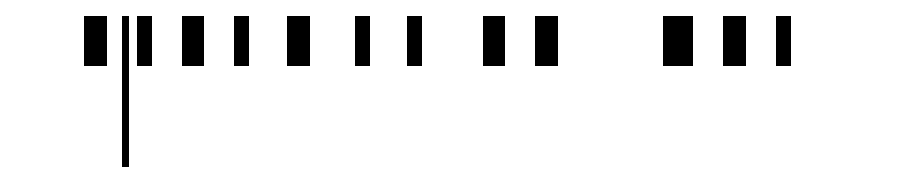

```mathematica
relaxation = Relax[4,disturbed];
ArrayPlot[relaxation]
```

```mathematica
relaxed = Last[relaxation];
ArrayPlot[CellularAutomaton[37,relaxed,100]]
```

-Graphics-

PUTA MADRE: Acabo de notar que por cada perturbación que se le hace, el tiempo de relajacion aumenta linealmente, lo que quiere decir que aquí nunca hay estados críticos. Vale verga la vida.